```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
```

```mathematica
ClearAll[partialTranspose]
partialTranspose[rho_,{dA_,dB_},sys_:2]:=Module[{tensor,newTensor},

(*Reshape rho into a tensor with indices {i,j,k,l}*)
tensor=ArrayReshape[rho,{dA,dB,dA,dB}];

(*Swap indices depending on which subsystem to transpose*)
newTensor=Switch[sys,1,
(*Partial transpose on subsystem A:swap i and k*)
Transpose[tensor,{3,2,1,4}],
(*Partial transpose on subsystem B:swap j and l*)
2,Transpose[tensor,{1,4,3,2}],
(*Error Message*)
_,Message[partialTranspose::sys,sys];Return[$Failed]];
(*Reshape back to a matrix*)
ArrayReshape[newTensor,{dA*dB,dA*dB}]
]
EntanglementNegativity[ρ_,{dA_,dB_},sys_:2]:=Module[{ρPT,negativity,traceNorm},
(*Compute the partial transpose of the density matrix*)
ρPT=partialTranspose[ρ,{dA,dB},sys];

(*Calculate the trace norm (sum of absolute eigenvalues)*)
traceNorm=Tr[MatrixFunction[Sqrt,ConjugateTranspose[ρPT].ρPT]];

(*Compute the negativity:(||ρPT||_1-1)/2*)
negativity=(traceNorm-1)/2]
TripartiteNeg[ρ_]:=Module[{matrici,matricipt1,matricipt2,matricipt3,negeig1,neg1,negeig2,neg2,negeig3,neg3,neg},
matrici=ρ;
matricipt1={{matrici[[1,1]],matrici[[1,2]],matrici[[1,3]],matrici[[1,4]],matrici[[5,1]],matrici[[5,2]],matrici[[5,3]],matrici[[5,4]]},{matrici[[2,1]],matrici[[2,2]],matrici[[2,3]],matrici[[2,4]],matrici[[6,1]],matrici[[6,2]],matrici[[6,3]],matrici[[6,4]]},{matrici[[3,1]],matrici[[3,2]],matrici[[3,3]],matrici[[3,4]],matrici[[7,1]],matrici[[7,2]],matrici[[7,3]],matrici[[7,4]]},{matrici[[4,1]],matrici[[4,2]],matrici[[4,3]],matrici[[4,4]],matrici[[8,1]],matrici[[8,2]],matrici[[8,3]],matrici[[8,4]]},{matrici[[1,5]],matrici[[1,6]],matrici[[1,7]],matrici[[1,8]],matrici[[5,5]],matrici[[5,6]],matrici[[5,7]],matrici[[5,8]]},{matrici[[2,5]],matrici[[2,6]],matrici[[2,7]],matrici[[2,8]],matrici[[6,5]],matrici[[6,6]],matrici[[6,7]],matrici[[6,8]]},{matrici[[3,5]],matrici[[3,6]],matrici[[3,7]],matrici[[3,8]],matrici[[7,5]],matrici[[7,6]],matrici[[7,7]],matrici[[7,8]]},{matrici[[4,5]],matrici[[4,6]],matrici[[4,7]],matrici[[4,8]],matrici[[8,5]],matrici[[8,6]],matrici[[8,7]],matrici[[8,8]]}};
matricipt2={{matrici[[1,1]],matrici[[1,2]],matrici[[3,1]],matrici[[3,2]],matrici[[1,5]],matrici[[1,6]],matrici[[3,5]],matrici[[3,6]]},{matrici[[2,1]],matrici[[2,2]],matrici[[4,1]],matrici[[4,2]],matrici[[2,5]],matrici[[2,6]],matrici[[4,5]],matrici[[4,6]]},{matrici[[1,3]],matrici[[1,4]],matrici[[3,3]],matrici[[3,4]],matrici[[1,7]],matrici[[1,8]],matrici[[3,7]],matrici[[3,8]]},{matrici[[2,3]],matrici[[2,4]],matrici[[4,3]],matrici[[4,4]],matrici[[2,7]],matrici[[2,8]],matrici[[4,7]],matrici[[4,8]]},{matrici[[5,1]],matrici[[5,2]],matrici[[7,1]],matrici[[7,2]],matrici[[5,5]],matrici[[5,6]],matrici[[7,5]],matrici[[7,6]]},{matrici[[6,1]],matrici[[6,2]],matrici[[8,1]],matrici[[8,2]],matrici[[6,5]],matrici[[6,6]],matrici[[8,5]],matrici[[8,6]]},{matrici[[5,3]],matrici[[5,4]],matrici[[7,3]],matrici[[7,4]],matrici[[5,7]],matrici[[5,8]],matrici[[7,7]],matrici[[7,8]]},{matrici[[6,3]],matrici[[6,4]],matrici[[8,3]],matrici[[8,4]],matrici[[6,7]],matrici[[6,8]],matrici[[8,7]],matrici[[8,8]]}};
matricipt3={{matrici[[1,1]],matrici[[2,1]],matrici[[1,3]],matrici[[2,3]],matrici[[1,5]],matrici[[2,5]],matrici[[1,7]],matrici[[2,7]]},{matrici[[1,2]],matrici[[2,2]],matrici[[1,4]],matrici[[2,4]],matrici[[1,6]],matrici[[2,6]],matrici[[1,8]],matrici[[2,8]]},{matrici[[3,1]],matrici[[4,1]],matrici[[3,3]],matrici[[4,3]],matrici[[3,5]],matrici[[4,5]],matrici[[3,7]],matrici[[4,7]]},{matrici[[3,2]],matrici[[4,2]],matrici[[3,4]],matrici[[4,4]],matrici[[3,6]],matrici[[4,6]],matrici[[3,8]],matrici[[4,8]]},{matrici[[5,1]],matrici[[6,1]],matrici[[5,3]],matrici[[6,3]],matrici[[5,5]],matrici[[6,5]],matrici[[5,7]],matrici[[6,7]]},{matrici[[5,2]],matrici[[6,2]],matrici[[5,4]],matrici[[6,4]],matrici[[5,6]],matrici[[6,6]],matrici[[5,8]],matrici[[6,8]]},{matrici[[7,1]],matrici[[8,1]],matrici[[7,3]],matrici[[8,3]],matrici[[7,5]],matrici[[8,5]],matrici[[7,7]],matrici[[8,7]]},{matrici[[7,2]],matrici[[8,2]],matrici[[7,4]],matrici[[8,4]],matrici[[7,6]],matrici[[8,6]],matrici[[7,8]],matrici[[8,8]]}};
(*Respective Negativities*)
negeig1=Select[Eigenvalues[matricipt1]//Chop,#<0&];
neg1=-Total[negeig1];
negeig2=Select[Eigenvalues[matricipt2]//Chop,#<0&];
neg2=-Total[negeig2];
negeig3=Select[Eigenvalues[matricipt3]//Chop,#<0&];
neg3=-Total[negeig3];
(*Tripartite Negativity*)
neg=(neg1 neg2 neg3)^(1/3)]
```

```mathematica
XXXNMSSNegativity[γ_,T_,deltas_,timesteps_]:=Module[{ρA1,ρA2,ρA,Ν,gDown,HIdown,gUp,HIup,USATotal,UTotalVarying,OverallSS,SystemSS,SteadyStateNegSA1,SteadyStateNegSA2,SteadyStateNegA1A2,MinNeg,MaxNeg,TriNeg,NegSA1Plot,NegSA2Plot,NegA1A2Plot,Neglegend,TriNegPlot,ω},
ρA1=out[Basis[2,2],Basis[2,2]];
ρA2=out[Basis[2,1],Basis[2,1]];
ρA= kron[ρA1,ρA2];
ω=1.;
Ν=1/(Exp[ω/T]-1);
(*Calculate the coupling constants*)
gDown=Sqrt[γ (Ν+1)];
(*Define the interaction Hamiltonian for down transition*)
HIdown=-(1/2)gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2]+KronEye[σz,5,1].KronEye[σz,5,2]);

(*Calculate the coupling constants for up transition*)
gUp=Sqrt[γ (Ν)];

(*Define the interaction Hamiltonian for up transition*)
HIup=-(1/2)gUp (KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3]+KronEye[σz,5,1].KronEye[σz,5,3]);

(*Define the total unitary operation for the system and ancillas*)
USATotal=MatrixExp[-ⅈ (HIdown+HIup) Sqrt[Δt]];

UTotalVarying=ParallelTable[((PartialSWAP[δ,3,5,5]).N[SWAP[3,5,5]]).((PartialSWAP[δ,2,4,5]).N[SWAP[2,4,5]]).MatrixExp[-ⅈ (HIdown+HIup) Sqrt[Δt]],{δ,deltas},{Δt,timesteps}];

OverallSS=ParallelTable[CollisionModelSteadyState[UTotalVarying[[i,j]],ρA],{i,1,Length[deltas]},{j,1,Length[timesteps]}];


SteadyStateNegSA1=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],EntanglementNegativity[PTr[OverallSS[[i,j]],{3}],{2,2},2]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;
SteadyStateNegSA2=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],EntanglementNegativity[PTr[OverallSS[[i,j]],{2}],{2,2},2]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;
SteadyStateNegA1A2=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],EntanglementNegativity[PTr[OverallSS[[i,j]],{1}],{2,2},2]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;
TriNeg=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],TripartiteNeg[OverallSS[[i,j]]]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;

{SteadyStateNegSA1,SteadyStateNegSA2,SteadyStateNegA1A2,TriNeg}
]
```

```mathematica
γ=1;
deltas= Range[0,1,0.005];
timesteps= Range[0.001,1,0.005];
```

```mathematica
XXXNegativityData=XXXNMSSNegativity[γ,0.5,deltas,timesteps];
```

Inverse::sing: Matrix {{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.000144958+1. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«30»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«20»,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}} is singular.

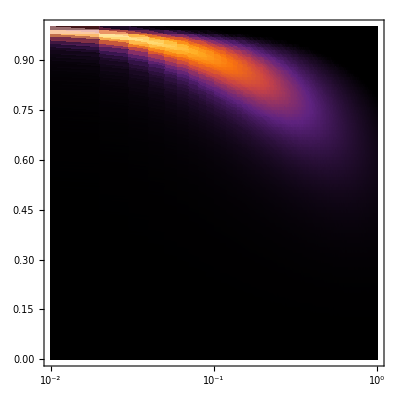

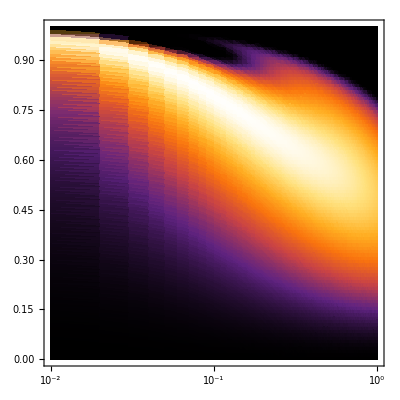

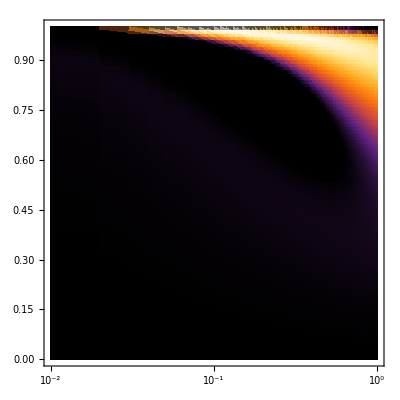

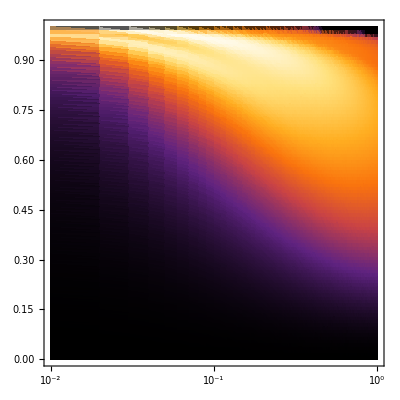

```mathematica
ListDensityPlot[XXXNegativityData[[1]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
ListDensityPlot[XXXNegativityData[[2]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
ListDensityPlot[XXXNegativityData[[3]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
ListDensityPlot[XXXNegativityData[[4]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
```

```mathematica
XXNMSSNegativity[γ_,T_,deltas_,timesteps_]:=Module[{ρA1,ρA2,ρA,Ν,gDown,HIdown,gUp,HIup,USATotal,UTotalVarying,OverallSS,SystemSS,SteadyStateNegSA1,SteadyStateNegSA2,SteadyStateNegA1A2,MinNeg,MaxNeg,TriNeg,NegSA1Plot,NegSA2Plot,NegA1A2Plot,Neglegend,TriNegPlot,ω},
ρA1=out[Basis[2,2],Basis[2,2]];
ρA2=out[Basis[2,1],Basis[2,1]];
ρA= kron[ρA1,ρA2];
ω=1.;
Ν=1/(Exp[ω/T]-1);
(*Calculate the coupling constants*)
gDown=Sqrt[γ (Ν+1)];
(*Define the interaction Hamiltonian for down transition*)
HIdown=-(1/2)gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2](*+KronEye[σz,5,1].KronEye[σz,5,2]*));

(*Calculate the coupling constants for up transition*)
gUp=Sqrt[γ (Ν)];

(*Define the interaction Hamiltonian for up transition*)
HIup=-(1/2)gUp (KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3](*+KronEye[σz,5,1].KronEye[σz,5,3]*));

(*Define the total unitary operation for the system and ancillas*)
USATotal=MatrixExp[-ⅈ (HIdown+HIup) Sqrt[Δt]];

UTotalVarying=ParallelTable[((PartialSWAP[δ,3,5,5]).N[SWAP[3,5,5]]).((PartialSWAP[δ,2,4,5]).N[SWAP[2,4,5]]).MatrixExp[-ⅈ (HIdown+HIup) Sqrt[Δt]],{δ,deltas},{Δt,timesteps}];

OverallSS=ParallelTable[CollisionModelSteadyState[UTotalVarying[[i,j]],ρA],{i,1,Length[deltas]},{j,1,Length[timesteps]}];

SteadyStateNegSA1=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],EntanglementNegativity[PTr[OverallSS[[i,j]],{3}],{2,2},2]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;
SteadyStateNegSA2=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],EntanglementNegativity[PTr[OverallSS[[i,j]],{2}],{2,2},2]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;
SteadyStateNegA1A2=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],EntanglementNegativity[PTr[OverallSS[[i,j]],{1}],{2,2},2]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;
TriNeg=Flatten[ParallelTable[{timesteps[[j]],deltas[[i]],TripartiteNeg[OverallSS[[i,j]]]},{i,1,Length[deltas]},{j,1,Length[timesteps]}],1]//Chop;
{SteadyStateNegSA1,SteadyStateNegSA2,SteadyStateNegA1A2,TriNeg}
]
```

```mathematica
XXNegativityData=XXNMSSNegativity[γ,0.5,deltas,timesteps]
```

Inverse::sing: Matrix … is singular.

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Wolfram/14.1/Executables/wolfram -noinit -subkernel -wstp,3959,18].

KernelObject::rdead: Subkernel connected through KernelObject[<|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,«26»,LaunchEvaluator→KernelConfiguration`nim[LaunchEvaluator],OneShotEvaluator→KernelObject`baseLinkEvaluate,Close→KernelObject`baseClose,OperatingSystem→Unix,LinkProtocol→Automatic,UseKernelForking→False,ForkingFunction→KernelObject`$DefaultForkingFunction,LowerPriority→True|>,«1»,«1»] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {322} assigned to KernelObject[<|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,«26»,LaunchEvaluator→KernelConfiguration`nim[LaunchEvaluator],OneShotEvaluator→KernelObject`baseLinkEvaluate,Close→KernelObject`baseClose,OperatingSystem→Unix,LinkProtocol→Automatic,UseKernelForking→False,ForkingFunction→KernelObject`$DefaultForkingFunction,LowerPriority→True|>,«1»,«1»].

LaunchKernels::clone: Kernel KernelObject[<|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,«26»,LaunchEvaluator→KernelConfiguration`nim[LaunchEvaluator],OneShotEvaluator→KernelObject`baseLinkEvaluate,Close→KernelObject`baseClose,OperatingSystem→Unix,LinkProtocol→Automatic,UseKernelForking→False,ForkingFunction→KernelObject`$DefaultForkingFunction,LowerPriority→True|>,«1»,«1»] resurrected as KernelObject[<|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,«26»,LaunchEvaluator→KernelConfiguration`nim[LaunchEvaluator],OneShotEvaluator→KernelObject`baseLinkEvaluate,Close→KernelObject`baseClose,OperatingSystem→Unix,LinkProtocol→Automatic,UseKernelForking→False,ForkingFunction→KernelObject`$DefaultForkingFunction,LowerPriority→True|>,«1»,«1»].

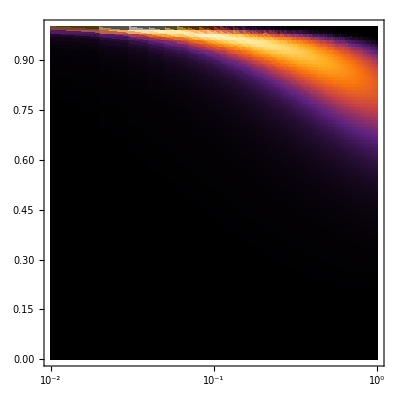

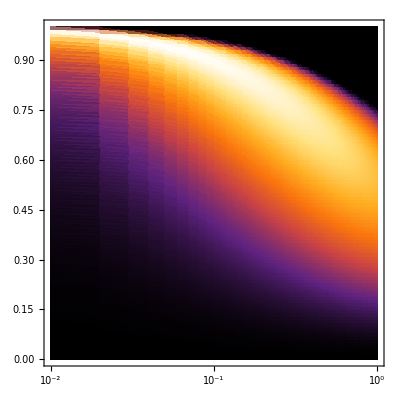

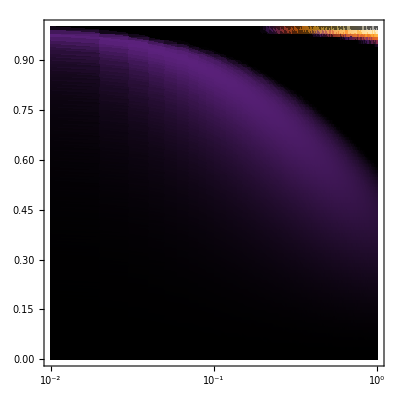

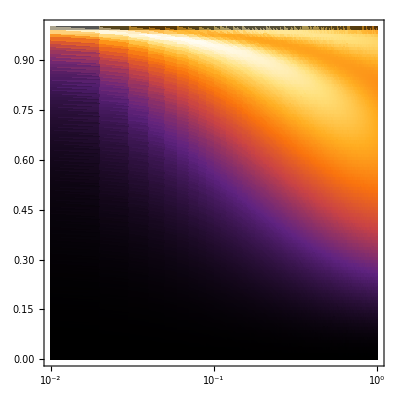

```mathematica
ListDensityPlot[XXNegativityData[[1]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
ListDensityPlot[XXNegativityData[[2]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
ListDensityPlot[XXNegativityData[[3]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
ListDensityPlot[XXNegativityData[[4]],PlotRange->All,ScalingFunctions->{"Log10",None},ColorFunction->"SunsetColors"]
```

```mathematica
(*Export["XXXSA1Negativity.mx",XXXNegativityData[[1]]]
Export["XXXSA2Negativity.mx",XXXNegativityData[[2]]]
Export["XXXA1A2Negativity.mx",XXXNegativityData[[3]]]
Export["XXXTriNegativity.mx",XXXNegativityData[[4]]]
*)
```

```mathematica
(*Export["XXSA1Negativity.mx",XXNegativityData[[1]]]
Export["XXSA2Negativity.mx",XXNegativityData[[2]]]
Export["XXA1A2Negativity.mx",XXNegativityData[[3]]]
Export["XXTriNegativity.mx",XXNegativityData[[4]]]*)
```